```mathematica
Dot[PauliMatrix[1], PauliMatrix[2]] // MatrixForm
Dot[PauliMatrix[2], PauliMatrix[1]] // MatrixForm
```

(ⅈ | 0
0 | -ⅈ)

(-ⅈ | 0
0 | ⅈ)

```mathematica
Dot[PauliMatrix[1], PauliMatrix[3]]
```

{{0,-1},{1,0}}

```mathematica
(1/2*(TensorProduct[IdentityMatrix[2], IdentityMatrix[2]]+Sum[TensorProduct[PauliMatrix[i],PauliMatrix[i]], {i, 1, 3}]))^2 // MatrixForm
```

((1 | 0
0 | 0) | (0 | 0
1 | 0)
(0 | 1
0 | 0) | (0 | 0
0 | 1))

```mathematica
TensorProduct[IdentityMatrix[2], IdentityMatrix[2]]+Sum[TensorProduct[PauliMatrix[i],PauliMatrix[i]], {i, 1, 3}] // MatrixForm
```

((2 | 0
0 | 0) | (0 | 0
2 | 0)
(0 | 2
0 | 0) | (0 | 0
0 | 2))

```mathematica
M = 1/2*(TensorProduct[IdentityMatrix[2], IdentityMatrix[2]]+Sum[TensorProduct[PauliMatrix[i],PauliMatrix[i]], {i, 1, 3}]);
M // MatrixForm
Dot[M, M] // MatrixForm
```

((1 | 0
0 | 0) | (0 | 0
1 | 0)
(0 | 1
0 | 0) | (0 | 0
0 | 1))

(((1 | 0
0 | 0) | (0 | 0
1 | 0)
(0 | 0
0 | 0) | (0 | 0
0 | 0)) | ((0 | 0
0 | 0) | (0 | 0
0 | 0)
(1 | 0
0 | 0) | (0 | 0
1 | 0))
((0 | 1
0 | 0) | (0 | 0
0 | 1)
(0 | 0
0 | 0) | (0 | 0
0 | 0)) | ((0 | 0
0 | 0) | (0 | 0
0 | 0)
(0 | 1
0 | 0) | (0 | 0
0 | 1)))

```mathematica
Sum[TensorProduct[PauliMatrix[i], IdentityMatrix[2]] + TensorProduct[IdentityMatrix[2],PauliMatrix[i]], {i, 1, 3}] // MatrixForm
```

((2 | 1-ⅈ
1+ⅈ | 0) | (1-ⅈ | 0
0 | 1-ⅈ)
(1+ⅈ | 0
0 | 1+ⅈ) | (0 | 1-ⅈ
1+ⅈ | -2))

```mathematica
TensorProduct[IdentityMatrix[2], IdentityMatrix[2]]// MatrixForm
```

((1 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 0
0 | 1))

```mathematica
F = 1/2*(TensorProduct[IdentityMatrix[2], IdentityMatrix[2]]+Sum[TensorProduct[PauliMatrix[i],PauliMatrix[i]], {i, 1, 3}]);
F // MatrixForm
F^2 // MatrixForm
```

((1 | 0
0 | 0) | (0 | 0
1 | 0)
(0 | 1
0 | 0) | (0 | 0
0 | 1))

((1 | 0
0 | 0) | (0 | 0
1 | 0)
(0 | 1
0 | 0) | (0 | 0
0 | 1))

```mathematica
Sum[Sum[Dot[PauliMatrix[i], PauliMatrix[j]], {i, 1,3}], {j,1,3}] // MatrixForm
```

(3 | 0
0 | 3)

```mathematica
LeviCivitaTensor[2] // MatrixForm
LeviCivitaTensor[3] // MatrixForm
```

(0 | 1
-1 | 0)

((0
0
0) | (0
0
1) | (0
-1
0)
(0
0
-1) | (0
0
0) | (1
0
0)
(0
1
0) | (-1
0
0) | (0
0
0))

```mathematica
F = 1/2*(TensorProduct[IdentityMatrix[2], IdentityMatrix[2]]+Sum[TensorProduct[PauliMatrix[i],PauliMatrix[i]], {i, 1, 3}]);
F // MatrixForm
```

((1 | 0
0 | 0) | (0 | 0
1 | 0)
(0 | 1
0 | 0) | (0 | 0
0 | 1))

```mathematica
P = {{1},{0}};
M = {{0},{1}};
F // MatrixForm
TensorProduct[P, P] // MatrixForm
```

((1 | 0
0 | 0) | (0 | 0
1 | 0)
(0 | 1
0 | 0) | (0 | 0
0 | 1))

((1
0)
(0
0))

```mathematica
TensorProduct[P, P] // MatrixForm
```

((1
0)
(0
0))

```mathematica
TensorProduct[IdentityMatrix[2], IdentityMatrix[2]] // MatrixForm
F^2 // MatrixForm
```

((1 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | (1 | 0
0 | 1))

((1 | 0
0 | 0) | (0 | 0
1 | 0)
(0 | 1
0 | 0) | (0 | 0
0 | 1))

```mathematica
TensorProduct[P, P] // MatrixForm
```

((1
0)
(0
0))

```mathematica
u = RandomReal[1,3];
v = RandomReal[1,3];
Trace[MatrixForm[u].Transpose[MatrixForm[v]]]-u.v
```

{{{-0.481237+u,-0.481237+{0.44757,0.588941,0.651067}},-0.481237+(0.44757
0.588941
0.651067)},{{{-0.481237+v,-0.481237+{0.153864,0.407861,0.264437}},-0.481237+(0.153864
0.407861
0.264437)},-0.481237+Transpose[(0.153864
0.407861
0.264437)]},-0.481237+(0.44757
0.588941
0.651067).Transpose[(0.153864
0.407861
0.264437)]}

```mathematica
u
u.v
u.Transpose[v]
```

{0.44757,0.588941,0.651067}

0.481237

(0.44757
0.588941
0.651067)

0.481237

```mathematica
RandomReal[1,3]
```

{0.1307,0.351254,0.96389}

```mathematica
L1 = hbar/Sqrt[2]*{{0,1,0},{1,0,1},{0,1,0}};
L2 = I*hbar/Sqrt[2]*{{0,-1,0},{1,0,-1},{0,1,0}};
```

```mathematica
L1.L2-L2.L1 // MatrixForm
```

(ⅈ hbar^2 | 0 | 0
0 | 0 | 0
0 | 0 | -ⅈ hbar^2)

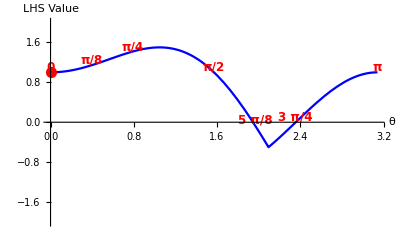

```mathematica
thetaValues={0,Pi/8,Pi/4,Pi/2,5 Pi/8,3 Pi/4,Pi};
labels={"0","π/8","π/4","π/2","5 π/8","3 π/4","π"};

lhs[θ_]:=Abs[-Cos[θ]+Cos[2 θ]]+Cos[θ]

Plot[lhs[θ],{θ,0,Pi},PlotStyle->Blue,AxesLabel->{"θ","LHS Value"},PlotRange->{All,{-2,2}},Ticks->{Automatic,Automatic,thetaValues},GridLines->{thetaValues,{1}},GridLinesStyle->Directive[Gray,Dashed],Epilog->{Red,PointSize[0.02],Point[{θ,lhs[θ]}/. Thread[θ->thetaValues]],Text[Style[labels[[#]],12,Bold],{thetaValues[[#]],lhs[thetaValues[[#]]]+0.1},{0,1}]&/@Range[7]}]
```